```mathematica
Clear["Global`*"];
```

```mathematica
no[λ_, T_] := Sqrt[4.9048 + 2.1429×10^-8(T^2-88506.25)+(0.11775+2.2314×10^-8(T^2-88506.25))/(λ^2-(0.21802-2.9671×10^-8(T^2-88506.25))^2)-0.027153 λ^2];
ne[λ_, T_] := Sqrt[4.5820 + 2.2971×10^-7(T^2-88506.25)+(0.09921+5.2716×10^-8(T^2-88506.25))/(λ^2-(0.21090-4.9143×10^-8(T^2-88506.25))^2)-0.021940 λ^2];
```

```mathematica
Plot[Evaluate[{no[λ,T],ne[λ,T]}/.{T->300}],{λ,0.5,1.5}];
```

```mathematica
neTheta[λ_,T_,θ_]:=(no[λ,T]ne[λ,T])/Sqrt[no[λ,T]^2-(no[λ,T]^2-ne[λ,T]^2)Cos[θ]^2];
```

```mathematica
Manipulate[Plot[Evaluate[neTheta[λ,T,θ]/.{T->300}],{λ,0.5,1.5}],{{θ,0},0,π}];
```

```mathematica
Θooe[λ_,T_]:= ArcCos[Chop[no[λ/2,T]/ne[λ,T]×Sqrt[(no[λ,T]^2-ne[λ/2,T]^2)/(no[λ/2,T]^2-ne[λ/2,T]^2)]]]×180/π;
```

```mathematica
a[λ_,T_] := no[λ/2,T]^2-ne[λ/2,T]^2;
Plot[a[1.178,T],{T,250,500}];
```

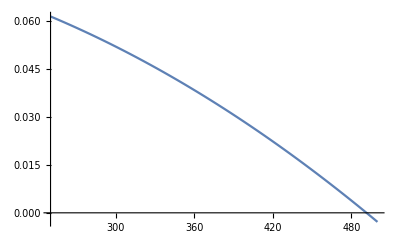

```mathematica
b[λ_,T_] := no[λ,T]^2-ne[λ/2,T]^2;
Plot[b[1.178,T],{T,250,500}]
```

```mathematica
f[λ_,T_] := (no[λ,T]^2-ne[λ/2,T]^2)/(no[λ/2,T]^2-ne[λ/2,T]^2);
Plot[f[1.178,T],{T,250,500}];
```

```mathematica
Θooe[1.178,300]
```

66.8746

```mathematica
Manipulate[Plot[Evaluate[Θooe[λ,T]],{T,250,500}],{{λ,1.178},0.4,4}]
```

```mathematica
Manipulate[Plot[Θooe[λ,T],{λ,1,1.5}],{{T,300},150,450}];
```

```mathematica
Θoee[λ_,T_] := 180/π×Θ/.FindRoot[no[λ,T]+neTheta[λ,T,Θ]==2neTheta[λ/2,T,Θ],{Θ,π/4}];
```

```mathematica
Off[FindRoot::lstol]
Θoee[1.178,300];
```